# Лабораторная работа №2 Вариант №13

Выполнил студент группы 0В92
Толстихин Илья

Импортируем котировки согласно 13 варианту (4, 9, 10, 11, 12, 13, 17)

```mathematica
X=Flatten[Import["D:\\Doc\\tpu\\многомерные статистические методы\\Cot.xlsx"],1]
```

{{0.0675,174.7,838.,24.97,1000.5,3.625,455.5},{0.06666,179.9,845.,25.3,1047.,3.79,476.7},{0.06741,190.05,876.,26.4,1060.,3.875,483.},{0.06531,195.,910.,26.5,1050.,4.045,475.1},{0.06353,193.,906.,26.4,1020.,3.885,470.7},{0.0605,204.5,903.,25.,1035.5,3.825,489.4},{0.0601,210.2,921.,25.25,1024.,3.885,497.9},{0.06273,216.5,960.,26.13,1045.,3.91,483.2},{0.06522,215.8,972.,26.28,1076.,3.96,490.},{0.06401,215.,951.,26.8,1090.,3.985,487.},{0.0621,214.15,964.,27.23,1119.,3.96,475.},{0.0635,222.95,960.,32.15,1120.,3.995,490.4},{0.06362,227.,1033.,35.55,1119.,3.995,523.7},{0.0638,228.,1012.,34.4,1070.,3.995,512.},{0.0626,214.25,1035.,32.71,1051.,3.9,504.},{0.06364,215.55,1011.,33.7,1040.,3.9,505.5},{0.06718,214.,959.,33.59,1055.,3.96,488.},{0.0665,219.55,935.,43.3,1055.,3.995,480.4},{0.06894,217.85,900.,44.85,1049.5,4.015,460.},{0.06696,227.3,904.,39.59,1046.5,4.115,472.},{0.0677,233.05,920.,39.1,1054.,4.06,482.3},{0.06689,232.,942.,40.89,1052.,4.04,478.5},{0.06786,235.5,995.,43.28,1061.,4.005,500.2},{0.06826,240.8,1085.,41.99,1060.,4.04,522.2},{0.068,240.6,1060.,43.,1069.,4.095,527.5},{0.06821,230.05,1032.,43.28,1063.,4.08,520.},{0.06905,237.95,1020.,43.31,1136.,5.685,530.9},{0.069,250.95,1025.,45.,1100.5,6.69,539.5},{0.0694,257.35,1079.,45.44,1112.,6.16,543.8},{0.06725,252.3,1041.,44.24,1150.,6.17,524.6},{0.06709,252.,1032.,46.6,1130.5,5.98,522.7},{0.06684,250.35,1060.,47.84,1118.5,6.47,527.5},{0.06696,257.,1040.,55.35,1110.,6.21,529.2},{0.0666,252.5,1020.,55.1,1096.,6.9,518.1},{0.06451,250.3,1034.,61.99,1100.,7.015,518.3},{0.0667,248.6,1015.,73.,1105.,6.92,506.7},{0.0701,253.5,1005.,83.58,1111.5,7.03,499.3},{0.068,249.,1014.,82.27,1110.,7.,503.7},{0.0681,247.55,1051.,83.,1130.,7.02,512.2},{0.06951,257.25,1041.,83.79,1138.,6.86,522.},{0.068,252.,1017.,89.45,1134.5,7.085,512.7},{0.0664,247.5,989.,93.5,1138.5,7.3,512.4},{0.06472,244.5,977.,77.49,1125.5,7.245,498.7},{0.0626,234.5,987.,70.04,1116.5,6.7,485.},{0.06328,234.,941.,88.,1118.,6.695,482.},{0.0645,232.35,922.,87.27,1125.5,6.63,471.8},{0.06332,230.3,920.,82.5,1116.,6.055,461.7},{0.0621,222.7,886.,73.78,1065.,5.89,466.},{0.061,220.4,868.,72.68,1000.,5.89,460.},{0.0624,227.3,891.,78.,998.,5.96,464.},{0.0623,227.,857.,80.05,1045.,5.945,447.},{0.0634,238.95,893.,70.54,1042.5,5.895,453.},{0.06172,238.75,908.,72.15,1008.,5.77,434.8},{0.063,246.,905.,72.19,1013.,5.77,429.4},{0.0628,249.65,906.,70.3,1001.5,5.795,430.3},{0.0606,242.75,897.,65.54,1002.,5.5,418.},{0.0595,243.,903.,60.11,1066.,5.39,416.5},{0.06002,246.3,932.,75.45,1028.,5.64,432.},{0.06,247.,915.,74.3,1016.5,5.605,432.},{0.06039,250.9,954.,71.2,1028.,5.69,450.3},{0.0617,250.,970.,71.8,1011.,6.08,467.2},{0.06162,248.6,958.,69.02,1013.,6.1,476.4},{0.0623,253.9,961.,70.42,1016.5,6.38,478.},{0.06014,255.,992.,69.87,1027.5,6.225,474.4},{0.06,253.,960.,71.53,1022.,6.055,470.6},{0.05879,252.,928.,67.85,1025.,6.14,465.5},{0.0587,248.,913.,66.97,1035.,5.94,463.6},{0.05903,253.1,920.,64.7,1059.5,6.055,477.2},{0.0579,253.5,915.,65.,1045.,5.995,462.9},{0.05826,263.,929.,66.38,1090.,6.095,480.7},{0.05891,263.7,940.,64.65,1120.5,6.195,493.},{0.05805,257.,918.,62.99,1143.,6.035,504.8},{0.058,252.9,921.,63.87,1175.,6.015,507.},{0.0585,255.15,936.,65.15,1220.,6.255,523.3},{0.05814,252.4,914.,63.9,1316.,6.17,505.1},{0.0569,253.25,886.,61.6,1270.5,5.94,499.6},{0.05984,255.15,885.,64.95,1324.5,6.045,498.9},{0.05991,257.8,870.,64.7,1400.,6.,496.4},{0.06215,261.,879.,64.01,1501.5,5.93,495.4},{0.0631,258.,870.,65.94,1515.,5.935,499.},{0.0655,265.,877.,64.3,1545.,5.955,494.},{0.06855,267.25,879.,65.2,1587.5,6.075,501.},{0.06831,262.55,870.,64.65,1610.,6.03,490.6},{0.06752,260.,858.,63.76,1665.5,5.965,490.},{0.0675,264.85,873.,63.49,1691.,5.99,502.7},{0.06647,266.3,865.,62.5,1590.,6.045,502.7},{0.066,271.,838.,61.29,1605.5,5.985,501.4},{0.06515,268.7,836.,62.08,1585.,5.935,500.9},{0.06843,269.05,847.,62.27,1600.,5.935,504.1},{0.071,267.65,835.,60.88,1613.5,5.92,502.},{0.07202,260.,831.,59.12,1621.5,5.85,495.5},{0.072,252.65,821.,64.6,1637.,5.86,494.7},{0.07507,251.,833.,63.4,1612.,5.895,508.6},{0.07777,252.5,835.,62.24,1612.,5.915,512.4},{0.0795,254.,834.,62.52,1607.5,5.91,506.8},{0.0815,249.4,829.,63.,1606.5,5.89,515.7},{0.0826,244.5,827.,62.08,1601.5,5.95,524.4},{0.0805,246.85,830.,63.15,1591.5,6.,528.5},{0.08025,243.,811.,65.25,1575.,5.95,522.5},{0.08035,241.4,817.,66.7,1567.,5.99,525.1},{0.08021,245.3,825.,67.8,1515.,5.995,536.3},{0.08105,241.05,829.,66.7,1510.,5.89,539.4},{0.08105,239.5,820.,66.82,1483.,5.84,538.2},{0.08107,239.3,822.,71.,1475.5,5.975,541.9},{0.0819,241.5,820.,72.14,1510.,5.95,541.2},{0.08175,241.5,813.,71.65,1540.,5.97,547.3},{0.08052,239.,789.,71.3,1640.,5.985,543.9},{0.0804,238.25,771.,71.33,1712.,5.89,543.5},{0.08039,241.6,767.,70.16,1798.5,5.81,550.9},{0.08,242.8,776.,70.13,1804.5,5.845,546.9},{0.08001,240.1,770.,69.99,1805.,5.795,545.},{0.0799,243.5,786.,71.5,1812.,5.785,540.},{0.08002,245.,796.,72.,1806.,5.765,547.1},{0.07951,253.1,797.,72.84,1804.5,5.78,546.4},{0.07839,250.5,798.,70.4,1800.5,5.725,544.5},{0.0779,248.35,784.,67.94,1804.,5.72,541.7},{0.078,246.05,787.,67.65,1800.,5.55,531.1},{0.078,248.8,776.,69.17,1795.,5.575,546.5},{0.07812,243.25,769.,70.01,1801.5,5.53,549.9},{0.079,243.1,778.,70.07,1710.,5.525,557.7},{0.07719,243.9,779.,71.6,1710.,5.525,560.6},{0.07746,245.85,771.,72.42,1730.,5.685,550.},{0.07584,243.95,757.,70.51,1690.,5.52,551.},{0.0745,222.05,758.,69.55,1710.,5.49,557.6},{0.0746,218.,755.,67.5,1706.,5.455,559.4},{0.07332,215.7,774.,63.16,1739.5,5.28,561.2},{0.07301,219.6,772.,64.25,1786.,5.25,564.7},{0.0752,220.25,789.,65.03,1801.,5.18,565.5},{0.07455,222.15,784.,64.79,1783.,5.225,575.},{0.07495,219.75,777.,64.4,1821.,5.19,577.7},{0.0749,218.2,785.,64.99,1824.,5.22,578.4},{0.07424,221.7,785.,67.2,1810.,5.355,577.7},{0.07401,219.9,819.,67.09,1830.,5.365,574.7},{0.07284,216.8,817.,67.19,1807.,5.265,570.},{0.07325,214.95,809.,67.17,1810.5,5.315,564.2},{0.07323,211.8,809.,65.9,1810.5,5.3,569.5},{0.07275,215.5,787.,64.85,1786.5,5.17,566.7},{0.0719,211.,776.,61.97,1777.,5.115,559.5},{0.0723,207.65,748.,59.18,1803.5,5.05,567.5},{0.07225,211.8,725.,59.46,1807.5,5.07,577.},{0.07229,217.05,736.,60.5,1805.,5.02,578.2},{0.07196,219.,758.,60.92,1805.,5.02,575.},{0.072,224.9,765.,61.03,1800.,5.1,591.},{0.072,222.55,770.,61.44,1800.,5.09,587.9},{0.071,222.25,785.,61.3,1815.,5.12,597.9},{0.071,227.1,792.,61.94,1835.,5.1,589.3},{0.07053,227.6,804.,60.95,1875.,5.095,593.3},{0.07081,229.65,830.,61.,2060.,5.095,598.},{0.07044,231.,825.,61.17,2280.,5.21,597.4},{0.0705,231.95,807.,60.77,2200.,5.195,592.5},{0.07024,230.,803.,60.39,2430.,5.17,597.5},{0.07054,229.5,809.,60.72,2360.,5.16,593.8},{0.07042,226.7,816.,60.6,2365.,5.15,590.7},{0.07035,230.1,802.,59.19,2260.,5.125,584.4},{0.06966,229.3,816.,58.7,2200.,5.045,584.},{0.06933,227.95,810.,56.81,2305.,5.04,571.7},{0.0694,232.,825.,55.96,2250.,5.07,586.},{0.0687,228.7,814.,53.95,2315.,5.03,564.},{0.06652,223.75,806.,51.2,2215.,4.855,567.2},{0.07,224.7,809.,56.9,2230.,4.87,560.3},{0.0698,221.,807.,57.36,2230.,4.92,581.2},{0.06985,227.25,801.,61.29,2280.,4.95,599.5},{0.06965,228.9,818.,64.39,2370.,4.96,613.9},{0.069,228.85,814.,68.39,2370.,4.93,633.},{0.06728,227.55,805.,68.54,2465.,4.94,610.},{0.06695,228.,806.,68.83,2500.,4.945,606.}}

Далее нормируем и центрируем, а также получим матрицу корреляции

```mathematica
X0=Standardize[X];
```

```mathematica
A=Covariance[X0];
MatrixForm[%]
k=7;
```

(1. | -0.0638074 | -0.596776 | 0.194687 | 0.548753 | 0.0383089 | 0.580469
-0.0638074 | 1. | 0.232473 | 0.495666 | -0.10795 | 0.721332 | -0.218395
-0.596776 | 0.232473 | 1. | -0.255166 | -0.75665 | 0.110546 | -0.540179
0.194687 | 0.495666 | -0.255166 | 1. | 0.208266 | 0.795481 | 0.0862348
0.548753 | -0.10795 | -0.75665 | 0.208266 | 1. | -0.0773293 | 0.849289
0.0383089 | 0.721332 | 0.110546 | 0.795481 | -0.0773293 | 1. | -0.106448
0.580469 | -0.218395 | -0.540179 | 0.0862348 | 0.849289 | -0.106448 | 1.)

Получим собственные значения и вектора

```mathematica
La=Eigenvalues[A]
```

{3.04577,2.36108,0.548104,0.511239,0.365053,0.107928,0.0608266}

```mathematica
Va = Eigenvectors[A]; TableForm[Va]
```

0.439836 | -0.148272 | -0.489912 | 0.113706 | 0.527925 | -0.0721557 | 0.497701
-0.0888787 | -0.529084 | 0.0190837 | -0.573973 | -0.0414267 | -0.616441 | 0.0254124
-0.106217 | 0.438521 | 0.535273 | -0.369193 | 0.272679 | 0.00349151 | 0.54702
0.861745 | 0.163202 | 0.160753 | -0.26635 | -0.342072 | 0.00628099 | -0.130091
-0.0974832 | 0.635336 | -0.464233 | -0.302299 | 0.215154 | -0.294409 | -0.383382
-0.120394 | -0.155428 | -0.328814 | -0.593674 | -0.0785046 | 0.70098 | 0.0569545
-0.144084 | 0.226584 | -0.351614 | 0.0809151 | -0.689752 | -0.191555 | 0.534105

Проверим на независимость:

Уровень значимости принятия гипотезы о независимости факторов очень мал, поэтому факторы зависимы.

Можно сделать вывод о том, что отбираем только первые 2 фактора(посмотрев на вектор собственных значений), так как для критерия Кайзера требуются наибольшие собственные значения. Оценим долю общей дисперсии:

```mathematica
Table[Sum[La[[i]]/k,{i,1,j}],{j,1,k}]
```

{0.43511,0.772407,0.850708,0.923742,0.975892,0.99131,1.}

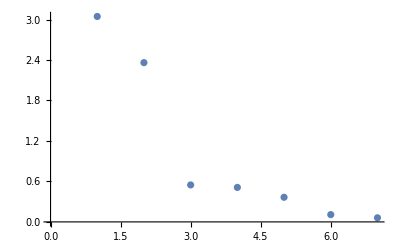

```mathematica
ListPlot[La]
```

Согласно методу каменистой осыпи, следует оставить 2-3 фактора

```mathematica
Table[Sum[1./i, {i,j,k}],{j,1,k}]
```

{2.59286,1.59286,1.09286,0.759524,0.509524,0.309524,0.142857}

```mathematica
Table[Sum[La[[i]]/k,{i,1,j}],{j,1,k}]
```

{0.43511,0.772407,0.850708,0.923742,0.975892,0.99131,1.}

Первый вектор отображает модель сломанной трости, второй же состоит из нормированных собственных чисел. Отбираем те факторы, которые больше факторов вектора модели сломанной трости - 3 фактора.

Основываясь на оценках, полученных всеми метода, сделаем вывод о том, что нужно остановиться на двух факторах.

```mathematica
B={Va[[1]],Va[[2]]}
```

{{0.439836,-0.148272,-0.489912,0.113706,0.527925,-0.0721557,0.497701},{-0.0888787,-0.529084,0.0190837,-0.573973,-0.0414267,-0.616441,0.0254124}}

Получим выражения для главных компонент:

```mathematica
{{Subscript[β, 1]=0.439 Subscript[e, 1], -0.148 Subscript[e, 2], -0.489 Subscript[e, 3], +0.1137 Subscript[e, 4], +0.5279 Subscript[e, 5], -0.07215 Subscript[e, 6], +0.497 Subscript[e, 7]}, {Subscript[β, 2]=-0.088 Subscript[e, 1], -0.529 Subscript[e, 2], +0.019 Subscript[e, 3], -0.574 Subscript[e, 4], -0.0414 Subscript[e, 5], -0.616 Subscript[e, 6], +0.0254 Subscript[e, 7]}}
```

Оценка значений главных компонент для наблюдений:

```mathematica
B1=Transpose[B]; X0.B1
```

{{-0.807007,4.65847},{-0.669342,4.3906},{-0.789614,3.98434},{-1.26808,3.74136},{-1.41844,3.94535},{-1.48149,3.75488},{-1.58026,3.54793},{-1.80197,3.27231},{-1.58978,3.22032},{-1.55984,3.21341},{-1.83819,3.25857},{-1.59365,2.76725},{-1.63824,2.54557},{-1.71462,2.55319},{-1.92219,3.1135},{-1.72154,3.01881},{-1.36415,2.95525},{-1.3307,2.38035},{-1.1787,2.30347},{-1.33365,2.19445},{-1.29957,2.08358},{-1.49346,2.0718},{-1.48448,1.90918},{-1.7765,1.80478},{-1.58236,1.73022},{-1.41152,2.02848},{-1.28494,0.598295},{-1.44793,-0.581474},{-1.66301,-0.389737},{-1.72293,-0.194576},{-1.69106,-0.138501},{-1.84429,-0.486651},{-1.69156,-0.793316},{-1.76605,-1.16304},{-1.91154,-1.42581},{-1.67226,-1.78292},{-1.43139,-2.48024},{-1.5445,-2.24118},{-1.60992,-2.23282},{-1.4063,-2.44837},{-1.40928,-2.67387},{-1.30779,-2.84564},{-1.61232,-2.06785},{-1.89512,-1.05276},{-1.48085,-1.76795},{-1.38259,-1.66921},{-1.54095,-0.985606},{-1.44217,-0.277967},{-1.55031,-0.152763},{-1.56569,-0.629937},{-1.48926,-0.71135},{-1.72325,-0.652359},{-2.1307,-0.59941},{-2.14128,-0.83565},{-2.21172,-0.882033},{-2.3939,-0.252218},{-2.47139,0.0457769},{-2.40577,-0.832733},{-2.33926,-0.78421},{-2.38147,-0.826444},{-2.24408,-1.11388},{-2.09347,-0.973681},{-2.10052,-1.39931},{-2.43926,-1.2634},{-2.27525,-1.15183},{-2.25739,-1.03276},{-2.14515,-0.736868},{-2.05495,-0.87941},{-2.26964,-0.851415},{-2.15172,-1.25595},{-2.02723,-1.284},{-1.7512,-0.892016},{-1.6651,-0.79208},{-1.51266,-1.08466},{-1.47137,-0.910814},{-1.51946,-0.663358},{-1.25904,-0.974574},{-1.12458,-1.02247},{-0.937123,-1.07613},{-0.729737,-1.08198},{-0.69926,-1.27388},{-0.40295,-1.50467},{-0.41477,-1.31796},{-0.318331,-1.1575},{-0.278297,-1.30002},{-0.452011,-1.32207},{-0.371666,-1.37007},{-0.417986,-1.28428},{-0.210943,-1.34313},{0.0207484,-1.27496},{0.105291,-0.947083},{0.272761,-0.959334},{0.528557,-0.917079},{0.713102,-0.963358},{0.756926,-1.04085},{1.05442,-0.932423},{1.25349,-0.805573},{1.11502,-0.922219},{1.17096,-0.857836},{1.18362,-0.895542},{1.16225,-1.04291},{1.25815,-0.804933},{1.27942,-0.727207},{1.32311,-0.983667},{1.41715,-1.09053},{1.54339,-1.08489},{1.69924,-1.00883},{1.8906,-0.927523},{2.06936,-0.925948},{1.94515,-0.981517},{1.9846,-0.86216},{1.82846,-1.01338},{1.84342,-1.05764},{1.73335,-1.33379},{1.63561,-1.10542},{1.6537,-0.939159},{1.55588,-0.740903},{1.76346,-0.894029},{1.91104,-0.732669},{1.89171,-0.723513},{1.80361,-0.781892},{1.75283,-1.00274},{1.69938,-0.726514},{1.87732,-0.00165302},{1.93523,0.22415},{1.8069,0.61181},{1.87202,0.476864},{1.95644,0.451771},{1.99977,0.386777},{2.16089,0.489645},{2.13951,0.492271},{2.04794,0.211875},{1.85061,0.268667},{1.74033,0.444405},{1.76421,0.452163},{1.83729,0.609559},{1.83963,0.640421},{1.77426,0.933652},{2.08576,1.18136},{2.2831,1.03386},{2.20393,0.877513},{2.01337,0.810785},{2.08878,0.584043},{2.05123,0.643707},{2.02765,0.656594},{1.88792,0.49791},{1.872,0.533297},{2.0109,0.457346},{2.26149,0.308247},{2.20295,0.307624},{2.563,0.381448},{2.4303,0.392527},{2.37956,0.48802},{2.21689,0.466955},{2.02482,0.586684},{2.03097,0.691228},{1.9957,0.599141},{1.86902,0.794054},{1.71406,1.21661},{1.90674,0.900415},{2.15964,0.968044},{2.43214,0.609151},{2.60197,0.43562},{2.82148,0.318713},{2.63924,0.342723},{2.61053,0.313273}}

Относительный вклад признака  в дисперсию главной компоненты  характеризует квадрат соответствующей координаты вектора . Таким образом, для каждой компоненты  отбираем признаки, которым соответствуют наибольшие абсолютные значения координат вектора , и определяем их суммарную долю вклада в компоненту, суммируя соответствующие квадраты координат.

```mathematica
B2={Va[[1]]*Va[[1]],Va[[2]]*Va[[2]]}
```

{{0.193455,0.0219844,0.240013,0.012929,0.278705,0.00520645,0.247706},{0.00789942,0.27993,0.000364187,0.329445,0.00171617,0.379999,0.000645788}}

Для первой компоненты наибольший вклад - первый, третий, пятый и седьмой признаки
	Для второй - второй, четвертый, шестой
Тогда суммарный вклад:

```mathematica
0.959866;
```

```mathematica
0.989365;
```